```mathematica
Braiding
```

```mathematica
* Define the patern by observing the 5 ropes
```

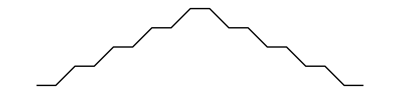

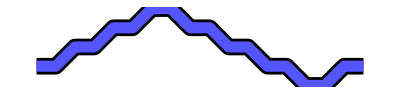

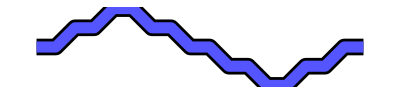

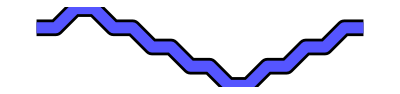

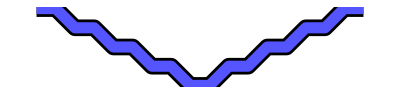

```mathematica
Rope1 = {{1, 2, 3, 4, 5, 4, 3, 2, 1}};
Rope2 = {{2, 3, 4, 5, 4, 3, 2, 1, 2}};
Rope3 = {{3, 4, 5, 4, 3, 2, 1, 2, 3}};
Rope4 = {{4, 5, 4, 3, 2, 1, 2, 3, 4}};
Rope5 = {{5, 4, 3, 2, 1, 2, 3, 4, 5}};
showBraid @ Rope1
ShowBraid @ Rope2
ShowBraid @ Rope3
ShowBraid @ Rope4
ShowBraid @ Rope5
```

```mathematica
* Assemble the 5 ropes into a braid
```

```mathematica
attempt 1
```

```mathematica
ClassicBraid1 = {{Rope1, Rope2, Rope3, Rope4, Rope5}};
```

```mathematica
showBraid @ ClassicBraid1
```

-Graphics-

```mathematica
attemp 2
```

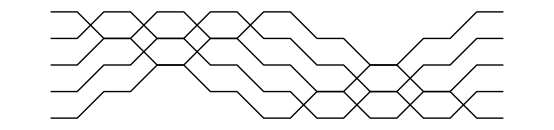

```mathematica
classicBraid2 = {{1, 2, 3, 4, 5, 4, 3, 2, 1}, {2, 3, 4, 5, 4, 3, 2, 1, 2}, {3, 4, 5, 4, 3, 2, 1, 2, 3}, {4, 5, 4, 3, 2, 1, 2, 3, 4}, {5, 4, 3, 2, 1, 2, 3, 4, 5}};
showBraid @ classicBraid2
```

```mathematica
ShowBraid[
	classicBraid2,
	CurveStyle -> Curvy
]
```

-Graphics-

```mathematica
attemp 3
```

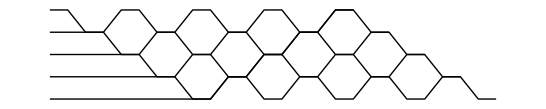

```mathematica
classicBraid3 = {{1,1, 1, 1,1, 2, 3, 4, 5, 4, 3, 2, 1}, {2, 2, 2,2,3, 4, 5, 4, 3, 2, 1, 2}, {3, 3,3, 4, 5, 4, 3, 2, 1, 2, 3}, {4, 4, 5, 4, 3, 2, 1, 2, 3, 4}, {5, 4, 3, 2, 1, 2, 3, 4, 5}};
showBraid @ classicBraid3
```

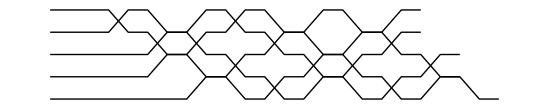

```mathematica
classicBraid4 = {{ 1, 1,1,1, 2, 3, 4, 5, 4, 3, 2, 1}, {2, 2,2,3, 4, 5, 4, 3, 2, 1, 2}, {3, 3,3, 4, 5, 4, 3, 2, 1, 2, 3}, {4, 4, 5, 4, 3, 2, 1, 2, 3, 4}, {5, 5, 4, 3, 2, 1, 2, 3, 4, 5}};
showBraid @ classicBraid4
```

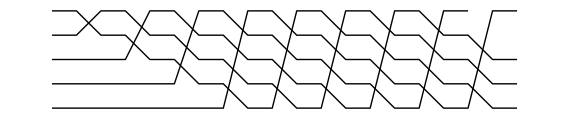

```mathematica
classicBraid5 = {{1,1, 1,1, 5, 4, 3, 2, 1, 5}, {2, 2,2, 5, 4, 3, 2, 1, 5}, {3,3, 5, 4, 3, 2, 1, 5, 4, 3}, { 4, 5, 4, 3, 2, 1,5, 4, 3, 2}, {5, 4, 3, 2, 1, 5, 4, 3, 2, 1}};
showBraid @ classicBraid5
```

```mathematica
*create an original patern
```

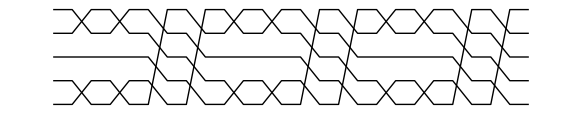

```mathematica
originalPatern= {{1,2,1,5, 4, 5,4,3, 2, 1, 2,1,5}, { 5,4, 5, 4, 3, 3, 3, 2, 1, 2,1,5, 4}, { 4, 5, 4, 3, 2, 1, 2, 1, 5, 4, 5,4, 3}, {  3,3,3, 2, 1,2,1,5, 4, 5, 4, 3, 2}, { 2, 1,2,1, 5, 4,5, 4, 3,3,3, 2, 1}};
showBraid @ originalPatern
```

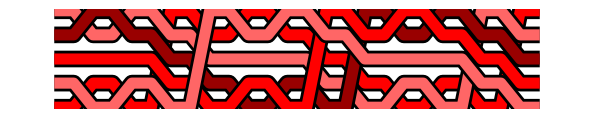

```mathematica
ShowBraid[
	originalPatern,
	CordStyles-> { Red, Lighter[Red, .4], Darker[Red, .4]}
]
```

```mathematica
originalPatern// MatrixForm
```

(1 | 2 | 1 | 5 | 4 | 5 | 4 | 3 | 2 | 1 | 2 | 1 | 5
5 | 4 | 5 | 4 | 3 | 3 | 3 | 2 | 1 | 2 | 1 | 5 | 4
4 | 5 | 4 | 3 | 2 | 1 | 2 | 1 | 5 | 4 | 5 | 4 | 3
3 | 3 | 3 | 2 | 1 | 2 | 1 | 5 | 4 | 5 | 4 | 3 | 2
2 | 1 | 2 | 1 | 5 | 4 | 5 | 4 | 3 | 3 | 3 | 2 | 1)

```mathematica
({{1, 2, 1, 5, 4, 5, 4, 3, 2, 1, 2, 1, 5}, {5, 4, 5, 4, 3, 3, 3, 2, 1, 2, 1, 5, 4}, {4, 5, 4, 3, 2, 1, 2, 1, 5, 4, 5, 4, 3}, {3, 3, 3, 2, 1, 2, 1, 5, 4, 5, 4, 3, 2}, {2, 1, 2, 1, 5, 4, 5, 4, 3, 3, 3, 2, 1}})
```

```mathematica
({{1, 2, 1, 5, 4, 5, 4, 3, 2, 1, 2, 1, 5}, {5, 4, 5, 4, 3, 3, 3, 2, 1, 2, 1, 5, 4}, {4, 5, 4, 3, 2, 1, 2, 1, 5, 4, 5, 4, 3}, {3, 3, 3, 2, 1, 2, 1, 5, 4, 5, 4, 3, 2}, {2, 1, 2, 1, 5, 4, 5, 4, 3, 3, 3, 2, 1}, {1, 2, 1, 5, 4, 5, 4, 3, 2, 1, 2, 1, 5}, {5, 4, 5, 4, 3, 3, 3, 2, 1, 2, 1, 5, 4}, {4, 5, 4, 3, 2, 1, 2, 1, 5, 4, 5, 4, 3}, {3, 3, 3, 2, 1, 2, 1, 5, 4, 5, 4, 3, 2}, {2, 1, 2, 1, 5, 4, 5, 4, 3, 3, 3, 2, 1}, {1, 2, 1, 5, 4, 5, 4, 3, 2, 1, 2, 1, 5}, {5, 4, 5, 4, 3, 3, 3, 2, 1, 2, 1, 5, 4}, {4, 5, 4, 3, 2, 1, 2, 1, 5, 4, 5, 4, 3}, {3, 3, 3, 2, 1, 2, 1, 5, 4, 5, 4, 3, 2}, {2, 1, 2, 1, 5, 4, 5, 4, 3, 3, 3, 2, 1}, {1, 2, 1, 5, 4, 5, 4, 3, 2, 1, 2, 1, 5}, {5, 4, 5, 4, 3, 3, 3, 2, 1, 2, 1, 5, 4}, {4, 5, 4, 3, 2, 1, 2, 1, 5, 4, 5, 4, 3}, {3, 3, 3, 2, 1, 2, 1, 5, 4, 5, 4, 3, 2}, {2, 1, 2, 1, 5, 4, 5, 4, 3, 3, 3, 2, 1}, {1, 2, 1, 5, 4, 5, 4, 3, 2, 1, 2, 1, 5}, {5, 4, 5, 4, 3, 3, 3, 2, 1, 2, 1, 5, 4}, {4, 5, 4, 3, 2, 1, 2, 1, 5, 4, 5, 4, 3}, {3, 3, 3, 2, 1, 2, 1, 5, 4, 5, 4, 3, 2}, {2, 1, 2, 1, 5, 4, 5, 4, 3, 3, 3, 2, 1}})
```

{{1,2,1,5,4,5,4,3,2,1,2,1,5},{5,4,5,4,3,3,3,2,1,2,1,5,4},{4,5,4,3,2,1,2,1,5,4,5,4,3},{3,3,3,2,1,2,1,5,4,5,4,3,2},{2,1,2,1,5,4,5,4,3,3,3,2,1},{1,2,1,5,4,5,4,3,2,1,2,1,5},{5,4,5,4,3,3,3,2,1,2,1,5,4},{4,5,4,3,2,1,2,1,5,4,5,4,3},{3,3,3,2,1,2,1,5,4,5,4,3,2},{2,1,2,1,5,4,5,4,3,3,3,2,1},{1,2,1,5,4,5,4,3,2,1,2,1,5},{5,4,5,4,3,3,3,2,1,2,1,5,4},{4,5,4,3,2,1,2,1,5,4,5,4,3},{3,3,3,2,1,2,1,5,4,5,4,3,2},{2,1,2,1,5,4,5,4,3,3,3,2,1},{1,2,1,5,4,5,4,3,2,1,2,1,5},{5,4,5,4,3,3,3,2,1,2,1,5,4},{4,5,4,3,2,1,2,1,5,4,5,4,3},{3,3,3,2,1,2,1,5,4,5,4,3,2},{2,1,2,1,5,4,5,4,3,3,3,2,1},{1,2,1,5,4,5,4,3,2,1,2,1,5},{5,4,5,4,3,3,3,2,1,2,1,5,4},{4,5,4,3,2,1,2,1,5,4,5,4,3},{3,3,3,2,1,2,1,5,4,5,4,3,2},{2,1,2,1,5,4,5,4,3,3,3,2,1}}

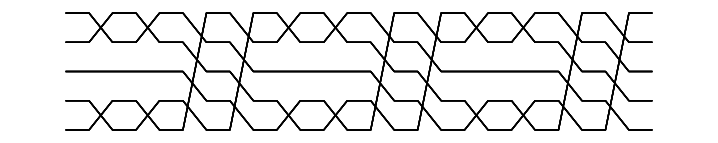

```mathematica
originalPatern2= {{1,2,1,5,4,5,4,3,2,1,2,1,5},{5,4,5,4,3,3,3,2,1,2,1,5,4},{4,5,4,3,2,1,2,1,5,4,5,4,3},{3,3,3,2,1,2,1,5,4,5,4,3,2},{2,1,2,1,5,4,5,4,3,3,3,2,1},{1,2,1,5,4,5,4,3,2,1,2,1,5},{5,4,5,4,3,3,3,2,1,2,1,5,4},{4,5,4,3,2,1,2,1,5,4,5,4,3},{3,3,3,2,1,2,1,5,4,5,4,3,2},{2,1,2,1,5,4,5,4,3,3,3,2,1},{1,2,1,5,4,5,4,3,2,1,2,1,5},{5,4,5,4,3,3,3,2,1,2,1,5,4},{4,5,4,3,2,1,2,1,5,4,5,4,3},{3,3,3,2,1,2,1,5,4,5,4,3,2},{2,1,2,1,5,4,5,4,3,3,3,2,1},{1,2,1,5,4,5,4,3,2,1,2,1,5},{5,4,5,4,3,3,3,2,1,2,1,5,4},{4,5,4,3,2,1,2,1,5,4,5,4,3},{3,3,3,2,1,2,1,5,4,5,4,3,2},{2,1,2,1,5,4,5,4,3,3,3,2,1},{1,2,1,5,4,5,4,3,2,1,2,1,5},{5,4,5,4,3,3,3,2,1,2,1,5,4},{4,5,4,3,2,1,2,1,5,4,5,4,3},{3,3,3,2,1,2,1,5,4,5,4,3,2},{2,1,2,1,5,4,5,4,3,3,3,2,1}};
showBraid @ originalPatern2
```

```mathematica
({{1, 2, 1, 5, 4, 5, 4, 3, 2, 1, 2, 1, 5}, {5, 4, 5, 4, 3, 3, 3, 2, 1, 2, 1, 5, 4}, {4, 5, 4, 3, 2, 1, 2, 1, 5, 4, 5, 4, 3}, {3, 3, 3, 2, 1, 2, 1, 5, 4, 5, 4, 3, 2}, {2, 1, 2, 1, 5, 4, 5, 4, 3, 3, 3, 2, 1}, {2, 1, 5, 4, 5, 4, 3, 2, 1, 2, 1, 5, 1}, {4, 5, 4, 3, 3, 3, 2, 1, 2, 1, 5, 4, 5}, {5, 4, 3, 2, 1, 2, 1, 5, 4, 5, 4, 3, 4}, {3, 3, 2, 1, 2, 1, 5, 4, 5, 4, 3, 2, 3}, {1, 2, 1, 5, 4, 5, 4, 3, 3, 3, 2, 1, 2}, {1, 5, 4, 5, 4, 3, 2, 1, 2, 1, 5, 1, 2}, {5, 4, 3, 3, 3, 2, 1, 2, 1, 5, 4, 5, 4}, {4, 3, 2, 1, 2, 1, 5, 4, 5, 4, 3, 4, 5}, {3, 2, 1, 2, 1, 5, 4, 5, 4, 3, 2, 3, 3}, {2, 1, 5, 4, 5, 4, 3, 3, 3, 2, 1, 2, 1}, {5, 4, 5, 4, 3, 2, 1, 2, 1, 5, 1, 2, 1}, {4, 3, 3, 3, 2, 1, 2, 1, 5, 4, 5, 4, 5}, {3, 2, 1, 2, 1, 5, 4, 5, 4, 3, 4, 5, 4}, {2, 1, 2, 1, 5, 4, 5, 4, 3, 2, 3, 3, 3}, {1, 5, 4, 5, 4, 3, 3, 3, 2, 1, 2, 1, 2}, {4, 5, 4, 3, 2, 1, 2, 1, 5, 1, 2, 1, 5}, {3, 3, 3, 2, 1, 2, 1, 5, 4, 5, 4, 5, 4}, {2, 1, 2, 1, 5, 4, 5, 4, 3, 4, 5, 4, 3}, {1, 2, 1, 5, 4, 5, 4, 3, 2, 3, 3, 3, 2}, {5, 4, 5, 4, 3, 3, 3, 2, 1, 2, 1, 2, 1}})
```

{{1,2,1,5,4,5,4,3,2,1,2,1,5},{5,4,5,4,3,3,3,2,1,2,1,5,4},{4,5,4,3,2,1,2,1,5,4,5,4,3},{3,3,3,2,1,2,1,5,4,5,4,3,2},{2,1,2,1,5,4,5,4,3,3,3,2,1},{2,1,5,4,5,4,3,2,1,2,1,5,1},{4,5,4,3,3,3,2,1,2,1,5,4,5},{5,4,3,2,1,2,1,5,4,5,4,3,4},{3,3,2,1,2,1,5,4,5,4,3,2,3},{1,2,1,5,4,5,4,3,3,3,2,1,2},{1,5,4,5,4,3,2,1,2,1,5,1,2},{5,4,3,3,3,2,1,2,1,5,4,5,4},{4,3,2,1,2,1,5,4,5,4,3,4,5},{3,2,1,2,1,5,4,5,4,3,2,3,3},{2,1,5,4,5,4,3,3,3,2,1,2,1},{5,4,5,4,3,2,1,2,1,5,1,2,1},{4,3,3,3,2,1,2,1,5,4,5,4,5},{3,2,1,2,1,5,4,5,4,3,4,5,4},{2,1,2,1,5,4,5,4,3,2,3,3,3},{1,5,4,5,4,3,3,3,2,1,2,1,2},{4,5,4,3,2,1,2,1,5,1,2,1,5},{3,3,3,2,1,2,1,5,4,5,4,5,4},{2,1,2,1,5,4,5,4,3,4,5,4,3},{1,2,1,5,4,5,4,3,2,3,3,3,2},{5,4,5,4,3,3,3,2,1,2,1,2,1}}

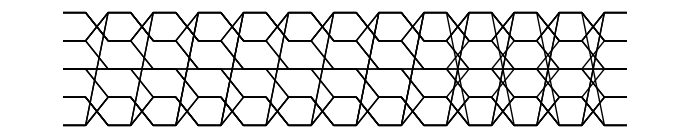

```mathematica
originalPatern3= {{1,2,1,5,4,5,4,3,2,1,2,1,5},{5,4,5,4,3,3,3,2,1,2,1,5,4},{4,5,4,3,2,1,2,1,5,4,5,4,3},{3,3,3,2,1,2,1,5,4,5,4,3,2},{2,1,2,1,5,4,5,4,3,3,3,2,1},{2,1,5,4,5,4,3,2,1,2,1,5,1},{4,5,4,3,3,3,2,1,2,1,5,4,5},{5,4,3,2,1,2,1,5,4,5,4,3,4},{3,3,2,1,2,1,5,4,5,4,3,2,3},{1,2,1,5,4,5,4,3,3,3,2,1,2},{1,5,4,5,4,3,2,1,2,1,5,1,2},{5,4,3,3,3,2,1,2,1,5,4,5,4},{4,3,2,1,2,1,5,4,5,4,3,4,5},{3,2,1,2,1,5,4,5,4,3,2,3,3},{2,1,5,4,5,4,3,3,3,2,1,2,1},{5,4,5,4,3,2,1,2,1,5,1,2,1},{4,3,3,3,2,1,2,1,5,4,5,4,5},{3,2,1,2,1,5,4,5,4,3,4,5,4},{2,1,2,1,5,4,5,4,3,2,3,3,3},{1,5,4,5,4,3,3,3,2,1,2,1,2},{4,5,4,3,2,1,2,1,5,1,2,1,5},{3,3,3,2,1,2,1,5,4,5,4,5,4},{2,1,2,1,5,4,5,4,3,4,5,4,3},{1,2,1,5,4,5,4,3,2,3,3,3,2},{5,4,5,4,3,3,3,2,1,2,1,2,1}};
showBraid @ originalPatern3
```

```mathematica
({{1, 2, 1, 5, 4, 5, 4, 3, 2, 1, 2, 1, 5, 1, 2, 1, 5, 4, 5, 4, 3, 2, 1, 2, 1, 5, 1, 2, 1, 5, 4, 5, 4, 3, 2, 1, 2, 1, 5, 1, 2, 1, 5, 4, 5, 4, 3, 2, 1, 2, 1, 5}, {5, 4, 5, 4, 3, 3, 3, 2, 1, 2, 1, 5, 4, 5, 4, 5, 4, 3, 3, 3, 2, 1, 2, 1, 5, 4, 5, 4, 5, 4, 3, 3, 3, 2, 1, 2, 1, 5, 4, 5, 4, 5, 4, 3, 3, 3, 2, 1, 2, 1, 5, 4}, {4, 5, 4, 3, 2, 1, 2, 1, 5, 4, 5, 4, 3, 4, 5, 4, 3, 2, 1, 2, 1, 5, 4, 5, 4, 3, 4, 5, 4, 3, 2, 1, 2, 1, 5, 4, 5, 4, 3, 4, 5, 4, 3, 2, 1, 2, 1, 5, 4, 5, 4, 3}, {3, 3, 3, 2, 1, 2, 1, 5, 4, 5, 4, 3, 2, 3, 3, 3, 2, 1, 2, 1, 5, 4, 5, 4, 3, 2, 3, 3, 3, 2, 1, 2, 1, 5, 4, 5, 4, 3, 2, 3, 3, 3, 2, 1, 2, 1, 5, 4, 5, 4, 3, 2}, {2, 1, 2, 1, 5, 4, 5, 4, 3, 3, 3, 2, 1, 2, 1, 2, 1, 5, 4, 5, 4, 3, 3, 3, 2, 1, 2, 1, 2, 1, 5, 4, 5, 4, 3, 3, 3, 2, 1, 2, 1, 2, 1, 5, 4, 5, 4, 3, 3, 3, 2, 1}})
```

{{1,2,1,5,4,5,4,3,2,1,2,1,5,1,2,1,5,4,5,4,3,2,1,2,1,5,1,2,1,5,4,5,4,3,2,1,2,1,5,1,2,1,5,4,5,4,3,2,1,2,1,5},{5,4,5,4,3,3,3,2,1,2,1,5,4,5,4,5,4,3,3,3,2,1,2,1,5,4,5,4,5,4,3,3,3,2,1,2,1,5,4,5,4,5,4,3,3,3,2,1,2,1,5,4},{4,5,4,3,2,1,2,1,5,4,5,4,3,4,5,4,3,2,1,2,1,5,4,5,4,3,4,5,4,3,2,1,2,1,5,4,5,4,3,4,5,4,3,2,1,2,1,5,4,5,4,3},{3,3,3,2,1,2,1,5,4,5,4,3,2,3,3,3,2,1,2,1,5,4,5,4,3,2,3,3,3,2,1,2,1,5,4,5,4,3,2,3,3,3,2,1,2,1,5,4,5,4,3,2},{2,1,2,1,5,4,5,4,3,3,3,2,1,2,1,2,1,5,4,5,4,3,3,3,2,1,2,1,2,1,5,4,5,4,3,3,3,2,1,2,1,2,1,5,4,5,4,3,3,3,2,1}}

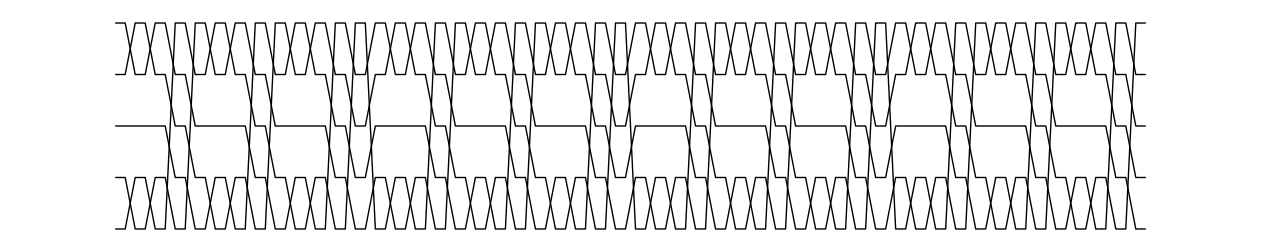

```mathematica
originalPatern4= {{1,2,1,5,4,5,4,3,2,1,2,1,5,1,2,1,5,4,5,4,3,2,1,2,1,5,1,2,1,5,4,5,4,3,2,1,2,1,5,1,2,1,5,4,5,4,3,2,1,2,1,5},{5,4,5,4,3,3,3,2,1,2,1,5,4,5,4,5,4,3,3,3,2,1,2,1,5,4,5,4,5,4,3,3,3,2,1,2,1,5,4,5,4,5,4,3,3,3,2,1,2,1,5,4},{4,5,4,3,2,1,2,1,5,4,5,4,3,4,5,4,3,2,1,2,1,5,4,5,4,3,4,5,4,3,2,1,2,1,5,4,5,4,3,4,5,4,3,2,1,2,1,5,4,5,4,3},{3,3,3,2,1,2,1,5,4,5,4,3,2,3,3,3,2,1,2,1,5,4,5,4,3,2,3,3,3,2,1,2,1,5,4,5,4,3,2,3,3,3,2,1,2,1,5,4,5,4,3,2},{2,1,2,1,5,4,5,4,3,3,3,2,1,2,1,2,1,5,4,5,4,3,3,3,2,1,2,1,2,1,5,4,5,4,3,3,3,2,1,2,1,2,1,5,4,5,4,3,3,3,2,1}};
showBraid @ originalPatern4
```

```mathematica
* vertical mirror image of the original braid
```

```mathematica
seq = originalPatern3
```

{{1,2,1,5,4,5,4,3,2,1,2,1,5},{5,4,5,4,3,3,3,2,1,2,1,5,4},{4,5,4,3,2,1,2,1,5,4,5,4,3},{3,3,3,2,1,2,1,5,4,5,4,3,2},{2,1,2,1,5,4,5,4,3,3,3,2,1},{2,1,5,4,5,4,3,2,1,2,1,5,1},{4,5,4,3,3,3,2,1,2,1,5,4,5},{5,4,3,2,1,2,1,5,4,5,4,3,4},{3,3,2,1,2,1,5,4,5,4,3,2,3},{1,2,1,5,4,5,4,3,3,3,2,1,2},{1,5,4,5,4,3,2,1,2,1,5,1,2},{5,4,3,3,3,2,1,2,1,5,4,5,4},{4,3,2,1,2,1,5,4,5,4,3,4,5},{3,2,1,2,1,5,4,5,4,3,2,3,3},{2,1,5,4,5,4,3,3,3,2,1,2,1},{5,4,5,4,3,2,1,2,1,5,1,2,1},{4,3,3,3,2,1,2,1,5,4,5,4,5},{3,2,1,2,1,5,4,5,4,3,4,5,4},{2,1,2,1,5,4,5,4,3,2,3,3,3},{1,5,4,5,4,3,3,3,2,1,2,1,2},{4,5,4,3,2,1,2,1,5,1,2,1,5},{3,3,3,2,1,2,1,5,4,5,4,5,4},{2,1,2,1,5,4,5,4,3,4,5,4,3},{1,2,1,5,4,5,4,3,2,3,3,3,2},{5,4,5,4,3,3,3,2,1,2,1,2,1}}

```mathematica
Show @ { showCord[seq] , showCord[Reverse[seq]] }
```

-Graphics-

```mathematica
Permutations = [originalPatern4]
```

```mathematica
Show @ { Permutations = [originalPatern4] }
```

```mathematica
* Study of KnotData
```

```mathematica
KnotData [originalPatern]
```

KnotData::notent: originalPatern is not a known entity, class, or tag for KnotData. Use KnotData[] for a list of entities.

KnotData[originalPatern]

```mathematica
KnotData[{"PretzelKnot", {5,3,2}}]
```

-Graphics3D-

```mathematica
KnotData[{"PretzelKnot", {5,5,5}}]
```

-Graphics3D-

```mathematica
KnotData[{4,1},"BraidImage"]
```

-Graphics3D-

```mathematica
KnotData[{4,1},"BraidWord"]
```

{{1,1},{2,-1},{1,1},{2,-1}}

```mathematica
KnotData[{8,2},"BraidImage"]
```

-Graphics3D-

```mathematica
KnotData[{8,2},"BraidWord"]
```

{{1,-1},{2,5},{1,-1},{2,1}}

```mathematica
KnotData[{8,8},"BraidImage"]
```

-Graphics3D-

```mathematica
KnotData[{8,8},"BraidWord"]
```

{{1,-1},{2,1},{1,2},{3,-1},{2,2},{3,-2}}

```mathematica
KnotData[{8,4},"BraidImage"]
```

-Graphics3D-

```mathematica
KnotData[{8,4},"BraidWord"]
```

{{1,3},{3,1},{2,-1},{3,-2},{1,1},{2,-1}}

```mathematica
KnotData[{10,6},"BraidImage"]
```

-Graphics3D-

```mathematica
KnotData[{10,6},"BraidWord"]
```

{{1,1},{2,-1},{3,1},{1,-1},{2,-1},{1,-1},{3,1},{2,6}}

```mathematica
KnotData[{10,4},"BraidImage"]
```

-Graphics3D-

```mathematica
KnotData[{10,4},"BraidWord"]
```

{{1,2},{4,-3},{2,1},{3,1},{2,-1},{1,-1},{4,-1},{3,1},{2,1}}

```mathematica
KnotData[{4,10},"BraidImage"]
```

KnotData::notent: {4, 10} is not a known entity, class, or tag for KnotData. Use KnotData[] for a list of entities.

KnotData[{4,10},BraidImage]

```mathematica
KnotData[{5,1},"BraidImage"]
```

-Graphics3D-

```mathematica
KnotData[{5,1},"BraidWord"]
```

{{1,5}}

```mathematica
KnotData[{10,4},{5, 1},"BraidImage"]
```

KnotData::notprop: {5, 1} is not a known property for KnotData. Use KnotData["Properties"] for a list of properties.

KnotData[{10,4},{5,1},BraidImage]

```mathematica
{1,2},{4,-3},{2,1},{3,1},{2,-1},{1,-1},{4,-1},{3,1},{2,1},{1,5},{1,1},{2,-1},{1,1},{2,-1}
```